# Algoritmo genético

## Definición del problema y codificación

```mathematica
CreateCities[n_]:=RandomReal[{0,100},{n,2}];
CreatePopulation[n_,cities_ :20]:=Table[RandomSample[Range[cities]],n];
OrderingPlot[cityMap_,ordering_,distance_]:=Show[
ListLinePlot[cityMap[[ordering]],
AspectRatio->1,
PlotRange->{{0,100},{0,100}},
ImageSize->500,
PlotTheme->"Monochrome",
FrameLabel->{Style["x",15],Style["y",15]},
Frame->True,BaseStyle->FontSize->14,
TicksStyle->Large,
PlotMarkers->None, 
PlotLabel->ToString[distance],
PlotStyle->Blue
],
ListPlot[cityMap,
PlotTheme->"Monochrome",
PlotMarkers->None,
PlotStyle->ColorData["Legacy"]["IndianRed"]
]
];
```

```mathematica
cityMap = CreateCities[20];
```

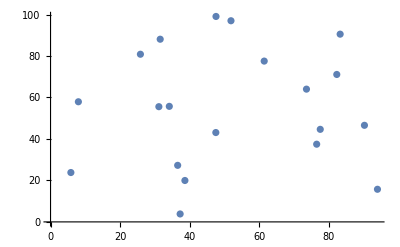

```mathematica
ListPlot[cityMap]
```

## Creación de población

```mathematica
CreatePopulation[n_,cities_ :20]:=Table[RandomSample[Range[cities]],n];
```

```mathematica
population = CreatePopulation[20,20]
```

{{15,2,20,16,19,1,13,12,4,7,17,5,9,8,14,18,11,3,10,6},{11,2,16,17,9,13,20,19,4,18,3,8,12,7,1,10,5,6,15,14},{3,17,15,7,20,18,2,11,5,9,10,8,19,4,6,16,12,14,13,1},{5,10,17,13,15,16,20,8,18,12,19,6,14,2,3,1,11,9,7,4},{13,9,1,17,11,2,5,12,10,4,14,15,20,7,18,16,19,6,3,8},{13,12,9,2,17,5,11,1,7,8,16,3,20,15,14,6,10,19,4,18},{19,7,18,17,4,11,8,14,15,6,12,10,2,5,1,13,20,9,16,3},{18,17,15,13,12,19,9,10,11,4,16,14,2,20,3,1,6,7,5,8},{2,10,1,3,5,16,15,11,18,7,13,4,20,9,8,12,17,14,19,6},{10,12,2,11,6,19,20,15,18,16,4,1,17,9,3,8,14,13,7,5},{11,19,18,7,6,13,4,1,17,2,12,5,20,16,10,8,15,9,3,14},{11,3,1,12,8,14,17,4,16,9,6,15,19,7,10,20,13,18,2,5},{1,2,20,5,6,16,10,11,7,3,14,19,18,4,9,15,13,8,17,12},{8,7,20,2,15,5,4,1,6,9,17,13,14,11,3,12,19,18,10,16},{1,6,11,16,9,7,14,8,18,15,5,2,10,4,17,19,20,13,12,3},{3,14,17,5,9,12,2,10,19,4,15,8,7,18,16,13,20,11,1,6},{15,14,3,1,19,18,16,17,13,2,7,6,12,8,11,9,10,20,5,4},{17,7,2,10,5,18,4,14,1,12,16,19,8,9,15,11,6,13,20,3},{6,20,4,12,14,16,15,7,8,11,13,1,3,5,19,18,17,2,10,9},{7,5,19,15,1,11,9,3,8,17,18,2,13,16,20,14,6,10,12,4}}

## Cálculo de rendimiento

```mathematica
Distace[{{x1_,y1_},{x2_,y2_}}]:=√((x1-x2)^2+(y1-y2)^2);
TotalDistance[cityMap_,ordering_]:=Total[Map[Distace,Partition[cityMap[[ordering]],2,1]]];

EvaluateGenome[cityMap_,population_]:=Map[<|"Genome"->#, "Distance"->TotalDistance[cityMap,#]|>&,population];
```

```mathematica
evaluated = EvaluateGenome[cityMap,population]
```

{<|Genome→{15,2,20,16,19,1,13,12,4,7,17,5,9,8,14,18,11,3,10,6},Distance→792.444|>,<|Genome→{11,2,16,17,9,13,20,19,4,18,3,8,12,7,1,10,5,6,15,14},Distance→850.634|>,<|Genome→{3,17,15,7,20,18,2,11,5,9,10,8,19,4,6,16,12,14,13,1},Distance→914.258|>,<|Genome→{5,10,17,13,15,16,20,8,18,12,19,6,14,2,3,1,11,9,7,4},Distance→870.075|>,<|Genome→{13,9,1,17,11,2,5,12,10,4,14,15,20,7,18,16,19,6,3,8},Distance→1040.35|>,<|Genome→{13,12,9,2,17,5,11,1,7,8,16,3,20,15,14,6,10,19,4,18},Distance→974.019|>,<|Genome→{19,7,18,17,4,11,8,14,15,6,12,10,2,5,1,13,20,9,16,3},Distance→932.231|>,<|Genome→{18,17,15,13,12,19,9,10,11,4,16,14,2,20,3,1,6,7,5,8},Distance→903.201|>,<|Genome→{2,10,1,3,5,16,15,11,18,7,13,4,20,9,8,12,17,14,19,6},Distance→898.915|>,<|Genome→{10,12,2,11,6,19,20,15,18,16,4,1,17,9,3,8,14,13,7,5},Distance→954.316|>,<|Genome→{11,19,18,7,6,13,4,1,17,2,12,5,20,16,10,8,15,9,3,14},Distance→1020.72|>,<|Genome→{11,3,1,12,8,14,17,4,16,9,6,15,19,7,10,20,13,18,2,5},Distance→941.062|>,<|Genome→{1,2,20,5,6,16,10,11,7,3,14,19,18,4,9,15,13,8,17,12},Distance→1023.91|>,<|Genome→{8,7,20,2,15,5,4,1,6,9,17,13,14,11,3,12,19,18,10,16},Distance→840.668|>,<|Genome→{1,6,11,16,9,7,14,8,18,15,5,2,10,4,17,19,20,13,12,3},Distance→802.869|>,<|Genome→{3,14,17,5,9,12,2,10,19,4,15,8,7,18,16,13,20,11,1,6},Distance→1109.37|>,<|Genome→{15,14,3,1,19,18,16,17,13,2,7,6,12,8,11,9,10,20,5,4},Distance→933.076|>,<|Genome→{17,7,2,10,5,18,4,14,1,12,16,19,8,9,15,11,6,13,20,3},Distance→964.8|>,<|Genome→{6,20,4,12,14,16,15,7,8,11,13,1,3,5,19,18,17,2,10,9},Distance→1017.5|>,<|Genome→{7,5,19,15,1,11,9,3,8,17,18,2,13,16,20,14,6,10,12,4},Distance→1039.12|>}

## Selección

```mathematica
ProportionateSelectionIndexes[population_,n_]:=RandomSample[Reverse[Range[population]]->Range[population],n];

ProportionateSelection[evaluatedGenome_,n_]:= Part[SortBy[evaluatedGenome,Key["Distance"]],ProportionateSelectionIndexes[Length[evaluatedGenome],n]]
```

```mathematica
fittest = ProportionateSelection[evaluated,4]
```

{<|Genome→{15,14,3,1,19,18,16,17,13,2,7,6,12,8,11,9,10,20,5,4},Distance→933.076|>,<|Genome→{17,7,2,10,5,18,4,14,1,12,16,19,8,9,15,11,6,13,20,3},Distance→964.8|>,<|Genome→{8,7,20,2,15,5,4,1,6,9,17,13,14,11,3,12,19,18,10,16},Distance→840.668|>,<|Genome→{19,7,18,17,4,11,8,14,15,6,12,10,2,5,1,13,20,9,16,3},Distance→932.231|>}

## Crossover

```mathematica
RandomSubsample[l_,n_]:=Block[{randomIndex},
randomIndex = RandomInteger[{1,Length[l]-n}];
{randomIndex,Take[l,{randomIndex,randomIndex+n-1}]}
];
ListInsert[list_,toInsert_,pos_]:=Block[{output},
output = list;
Do[
output[[i]] = toInsert[[i-pos+1]];
,
{i,pos,pos+Length[toInsert]-1,1}
];
Return[output];
];
```

```mathematica
IsInSwath[index_,swathLength_,position_]:=IntervalMemberQ[Interval[{index,index+swathLength-1}],position];
IsInChild[child_,allele_]:=MemberQ[child,allele];
Parent2Swath[parent2_,index_,length_]:=Take[parent2,{index,index+length-1}];
PairPositionAllele[parent1_,parent2_,allele_]:=Block[{pair},
pair = First[Extract[parent1,Position[parent2,allele]]];
{First@FirstPosition[parent2,pair],pair}
];
GetPositionInChild[parent1_,parent2_,swathIndex_,swath_,allele_]:=Block[{position,alleleValue},
{position,alleleValue} = PairPositionAllele[parent1,parent2,allele];
If[IsInSwath[swathIndex,Length[swath],position],
GetPositionInChild[parent1,parent2,swathIndex,swath,alleleValue],
position
]
];
```

```mathematica
PMXCrossover[parent1_,parent2_,subsampleSize_]:=Block[{swathIndex,swath,child,parent2Swath,position},
{swathIndex,swath} = RandomSubsample[parent1,subsampleSize];
child = ConstantArray[Null,Length[parent1]];
child = ListInsert[child,swath,swathIndex];
parent2Swath = Parent2Swath[parent2,swathIndex,Length[swath]];

Do[
If[!IsInChild[child,allele],
position = GetPositionInChild[parent1,parent2,swathIndex,swath,allele];
child[[position]] = allele;
];
,
{allele,parent2Swath}
];

child = Table[If[child[[i]]===Null,parent2[[i]],child[[i]]],{i,1,Length[child]}];
Return[child];
];
PopulationPMXCrossover[population_,subsampleSize_,childrenPerCouple_]:=Block[{couples,newGeneration},
couples = Partition[RandomSample[population],2];
newGeneration = Flatten[
Map[
Table[
PMXCrossover[First[#],Last[#],subsampleSize],
childrenPerCouple
]&,
couples
],1];
Return[newGeneration];
];
```

```mathematica
parent1 = {8,4,7,3,6,2,5,1,9,0};
parent2 = {0,1,2,3,4,5,6,7,8,9};
```

```mathematica
PMXCrossover[parent1,parent2,5]
```

{0,7,4,3,6,2,5,1,8,9}

```mathematica
newGeneration = PopulationPMXCrossover[fittest[[All,"Genome"]],10,10]
```

{{17,7,2,10,5,18,4,14,1,12,16,19,11,8,15,13,20,9,6,3},{17,7,2,10,5,18,4,14,1,12,16,19,11,8,15,13,20,9,6,3},{17,7,11,10,5,18,4,14,1,12,16,19,8,2,15,13,20,9,6,3},{10,7,11,17,2,18,4,14,1,12,16,19,8,9,15,13,20,5,6,3},{10,7,18,17,4,5,2,14,1,12,16,19,8,9,15,11,6,13,20,3},{10,7,18,17,4,5,2,14,1,12,16,19,8,9,15,11,6,13,20,3},{17,7,2,10,5,18,4,14,1,12,16,19,11,8,15,13,20,9,6,3},{10,7,18,17,2,13,4,14,1,12,16,19,8,9,15,11,20,5,6,3},{10,7,18,17,4,5,2,14,1,12,16,19,8,9,15,11,6,13,20,3},{17,7,11,10,5,18,4,14,1,12,16,19,8,2,15,13,20,9,6,3},{3,17,18,14,15,19,4,1,13,2,7,6,12,8,11,9,10,20,5,16},{8,9,3,1,19,18,16,17,13,2,7,6,14,11,20,12,15,5,10,4},{15,14,3,1,19,18,16,17,13,2,9,6,7,11,20,12,8,5,10,4},{3,1,20,9,15,18,16,17,13,2,7,6,12,8,11,14,19,5,10,4},{8,9,3,1,19,18,16,17,13,2,7,6,14,11,20,12,15,5,10,4},{8,14,3,1,19,18,16,17,13,2,7,6,9,11,20,12,15,5,10,4},{3,17,18,14,15,19,4,1,13,2,7,6,12,8,11,9,10,20,5,16},{3,1,20,9,15,18,16,17,13,2,7,6,12,8,11,14,19,5,10,4},{15,14,3,1,19,18,16,17,13,2,9,6,7,11,20,12,8,5,10,4},{8,14,3,1,19,18,16,17,13,2,7,6,9,11,20,12,15,5,10,4}}

## Mutación

```mathematica
RandomSwap[list_,probability_]:=Block[{newList,index1,index2},
If[RandomReal[]<probability,
{index1,index2} = RandomSample[Range[Length[list]],2];
newList = list;
newList[[index1]] = list[[index2]];
newList[[index2]] = list[[index1]];
Return[newList];
,
Return[list]
]
];
PopulationMutate[population_,probability_]:=Map[RandomSwap[#,probability]&,population];
```

```mathematica
PopulationMutate[newGeneration,0.1]
```

{{17,7,20,10,5,18,4,14,1,12,16,19,11,8,15,13,2,9,6,3},{17,7,2,10,5,18,4,14,1,12,16,19,11,8,15,13,20,9,6,3},{17,7,11,10,5,18,4,14,1,12,16,19,8,2,15,13,20,9,6,3},{10,7,11,17,2,18,4,14,1,12,16,19,8,9,15,13,20,5,6,3},{10,7,18,17,4,5,2,14,1,12,16,19,8,9,15,11,6,13,20,3},{10,7,18,17,4,5,2,14,1,12,16,19,8,9,15,11,6,13,20,3},{17,7,2,10,5,18,4,14,1,12,16,19,11,8,15,13,20,9,6,3},{10,6,18,17,2,13,4,14,1,12,16,19,8,9,15,11,20,5,7,3},{10,7,18,17,4,5,2,14,1,12,16,19,8,9,15,11,6,13,20,3},{17,7,11,10,5,18,4,14,1,12,16,19,8,2,15,13,20,9,6,3},{3,17,18,14,15,19,4,1,13,2,7,6,12,8,11,9,10,20,5,16},{8,9,3,1,19,18,16,17,13,2,7,6,14,11,20,12,15,5,10,4},{15,14,3,1,19,18,16,17,13,2,9,6,7,11,20,12,8,5,10,4},{3,1,20,9,15,18,16,17,13,2,7,6,12,8,11,14,19,5,10,4},{8,9,3,1,19,18,16,17,13,2,7,6,14,11,20,12,15,5,10,4},{8,14,3,1,19,18,16,17,13,2,7,6,9,11,20,12,15,5,10,4},{3,17,18,14,15,19,4,1,13,2,7,6,12,8,11,9,10,20,5,16},{3,1,20,9,15,18,16,17,13,2,7,6,12,8,11,14,19,5,10,4},{15,14,3,1,19,18,16,17,13,2,9,6,7,11,20,12,8,5,10,4},{8,14,3,1,19,18,16,17,13,2,7,6,9,11,20,12,15,5,10,4}}

## Algoritmo principal

```mathematica
Generation[cityMap_,population_,survivors_,crossoverSampleSize_,childrenPerCouple_,mutationProb_]:=Block[{evaluated,fittest,newGeneration},
evaluated = EvaluateGenome[cityMap,population];
fittest = ProportionateSelection[evaluated,survivors];
newGeneration = PopulationPMXCrossover[fittest[[All,"Genome"]],crossoverSampleSize,childrenPerCouple];
PopulationMutate[newGeneration,mutationProb]
];
GeneticAlgorithm[cityMap_,population_,survivors_,crossoverSampleSize_,childrenPerCouple_,mutationProb_,generations_]:=NestList[Generation[cityMap,#,survivors,crossoverSampleSize,childrenPerCouple,mutationProb]&,population,generations];
PlotBest[cityMap_,population_]:=Block[{min},
min = First@MinimalBy[EvaluateGenome[cityMap,population],Key["Distance"]];
OrderingPlot[cityMap,min["Genome"],min["Distance"]]
];
```

```mathematica
cityMap = CreateCities[20];
```

```mathematica
population = CreatePopulation[20,20];
```

```mathematica
generations = GeneticAlgorithm[cityMap,population,4,10,10,0.1,200];
```

```mathematica
plots = Map[PlotBest[cityMap,#]&,generations];
```

```mathematica
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```